```mathematica
Quit[]
```

#### Get component function (temporary)

```mathematica
Needs["Olveretal`"];
ClearAll[GetComponent]
Options[GetComponent]={Coordinates->"Spherical",Mute->True};
GetComponent[solvec_List,expr_List,layer_Integer,layout_List,n_Integer,OptionsPattern[]]:=
Block[{position,subdomain,nsubdomains,partition,zeroInDomain,startindex,listParity,listExtracted,(*options*) coordinates},

(* set up options *)
coordinates=OptionValue[Coordinates];
If[!OptionValue[Mute],
If[SameQ[coordinates,"Spheroidal"],Print["Spheroidal coordinates"],Print["Spherical coordinates"]]
];

(* recover subdomains from model *)
partition=Partition[Sort(*@Rest*)[Sprouts`domain],2,1];
nsubdomains=Length[partition];
Table[subdomain[i]=partition⟦i⟧,{i,1,Length[partition]}];
If[SameQ[N@First[subdomain[1]],0.],zeroInDomain=True,zeroInDomain=False];

(* find component position in solution vector *)
position=Flatten@Position[layout,Alternatives@@expr];

(* find parity of fields accross the origin based on their indices of spherical harmonics *)
listParity=
Block[{out},
If[zeroInDomain&&SameQ[layer,1],
Which[
SameQ[coordinates,"Spheroidal"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ+𝓂]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ+𝓂]],out="odd";,
True,Print["error with parity !"]
],
SameQ[coordinates,"Spherical"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ]],out="odd";,
True,Print["error with parity !"];
],
True,Print["error with coordinates !"];
]
];
out
]&/@expr;

(* extracted elements from solution vector *)
listExtracted=
Block[{extracted},
If[zeroInDomain,
startindex=Max[(layer-3/2)*n*Length[layout]+1,1];
If[SameQ[layer,1],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n/2-1⟧,{(#-1)*n/2+1,#*n/2}],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
],
startindex=(layer-1)*n*Length[layout]+1;
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
]
]&/@position;

(* output: riffle with zeroes if zero is in first layer *)
If[zeroInDomain&&SameQ[layer,1],
Table[
Switch[listParity⟦i⟧,
"even",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ],
"odd",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ,{1,-1,2}],
True,Print["error with Riffle !"]
]
,{i,1,Length[expr]}],
N@listExtracted
]

]
```

Get::noopen: Cannot open Olveretal`.

Needs::nocont: Context Olveretal` was not created when Needs was evaluated.

# Inviscid Navier-Stokes

## Load fennec & spectral package

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["spectral`","../spectral.m"];
Needs["sprouts`","../sprouts.m"];
```

## Components of vorticity and thermal equations

### two curls

```mathematica
rCurlCurlInertia[ℓ_,𝓂_]:=(ℓ^2 (1+ℓ)^2 P[ℓ,𝓂][r])/r^2-(2 ℓ (1+ℓ) P[ℓ,𝓂]'[r])/r-ℓ (1+ℓ) P[ℓ,𝓂]''[r];
rCurlCurlCoriolis[ℓ_,𝓂_]:=2(-(ℓ (1+2 ℓ) (-√((ℓ (-1+ℓ^2))/(-1+4 ℓ^2))+√((1-ℓ^2)/(ℓ-4 ℓ^3))) √(-((-1+ℓ^2) (ℓ-𝓂) (ℓ+𝓂))/(ℓ-4 ℓ^3)) T[-1+ℓ,𝓂][r])/r-ℓ (1+2 ℓ) √((1-ℓ^2)/(ℓ-4 ℓ^3)) √(-((-1+ℓ^2) (ℓ-𝓂) (ℓ+𝓂))/(ℓ-4 ℓ^3)) T[-1+ℓ,𝓂]'[r]-(ⅈ ℓ (1+ℓ) 𝓂 P[ℓ,𝓂][r])/r^2+(2 ⅈ 𝓂 P[ℓ,𝓂]'[r])/r+ⅈ 𝓂 P[ℓ,𝓂]''[r]-((1+ℓ) (1+2 ℓ) (√((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3))+√((ℓ (1+ℓ) (2+ℓ))/(3+4 ℓ (2+ℓ)))) √((ℓ (2+ℓ) (1+ℓ-𝓂) (1+ℓ+𝓂))/((1+ℓ) (1+2 ℓ) (3+2 ℓ))) T[1+ℓ,𝓂][r])/r-(1+ℓ) (1+2 ℓ) √((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3)) √((ℓ (2+ℓ) (1+ℓ-𝓂) (1+ℓ+𝓂))/((1+ℓ) (1+2 ℓ) (3+2 ℓ))) T[1+ℓ,𝓂]'[r]);
rCurlCurlViscosity[ℓ_,𝓂_]:=-1/r^4 ℓ (1+ℓ) ((-1+ℓ) ℓ (1+ℓ) (2+ℓ) P[ℓ,𝓂][r]+r^2 (-2 ℓ (1+ℓ) P[ℓ,𝓂]''[r]+r (4 P[ℓ,𝓂]'''[r]+r P[ℓ,𝓂]''''[r])));
```

### one curl

```mathematica
rCurlInertia[ℓ_,𝓂_]:=ℓ (1+ℓ) T[ℓ,𝓂][r];
rCurlCoriolis[ℓ_,𝓂_]:=2(((-1+ℓ)^2 (1+ℓ) √((ℓ-𝓂) (ℓ+𝓂)) P[-1+ℓ,𝓂][r])/(r (-1+2 ℓ))-((-1+ℓ^2) √((ℓ-𝓂) (ℓ+𝓂)) P[-1+ℓ,𝓂]'[r])/(-1+2 ℓ)-(ℓ (2+ℓ)^2 √((1+ℓ-𝓂) (1+ℓ+𝓂)) P[1+ℓ,𝓂][r])/(r (3+2 ℓ))-(ℓ (2+ℓ) √((1+ℓ-𝓂) (1+ℓ+𝓂)) P[1+ℓ,𝓂]'[r])/(3+2 ℓ)-ⅈ 𝓂 T[ℓ,𝓂][r]);
rCurlViscosity[ℓ_,𝓂_]:=(ℓ (1+ℓ) (-ℓ (1+ℓ) T[ℓ,𝓂][r]+r (2 T[ℓ,𝓂]'[r]+r T[ℓ,𝓂]''[r])))/r^2;
```

### putting things together

```mathematica
Ek=0 10^-4;ω=2/3+10^-1 ⅈ;ricb=0.35;
```

```mathematica
ClearAll[eqNS1,eqNS2]
eqNS1[ℓ_,𝓂_]:=ω rCurlCurlInertia[ℓ,𝓂]+rCurlCurlCoriolis[ℓ,𝓂](*-Ek rCurlCurlViscosity[ℓ,𝓂]*)==0
eqNS2[ℓ_,𝓂_]:=ω rCurlInertia[ℓ,𝓂]+rCurlCoriolis[ℓ,𝓂](*-Ek rCurlViscosity[ℓ,𝓂]*)==0
```

## Call to fennec

```mathematica
With[{𝓂=2,ℓmin=2,ℓmax=9},
listNS1=Table[Simplify[eqNS1[ℓ,𝓂]],{ℓ,ℓmin,ℓmax-1,2}]/.Derivative[n_][f_[ℓ_,𝓂_]][r]/;ℓ>ℓmax->0/.f_[ℓ_,𝓂_][r]/;ℓ>ℓmax->0;
listNS2=Table[Simplify[eqNS2[ℓ,𝓂]],{ℓ,ℓmin+1,ℓmax,2}]/.Derivative[n_][f_[ℓ_,𝓂_]][r]/;ℓ>ℓmax->0/.f_[ℓ_,𝓂_][r]/;ℓ>ℓmax->0;;
listpol=Table[Simplify[P[ℓ,𝓂]],{ℓ,ℓmin,ℓmax-1,2}];
listtor=Table[Simplify[T[ℓ,𝓂]],{ℓ,ℓmin+1,ℓmax,2}];
If[ricb==0,
listbc=Table[P[ℓ,𝓂][1]-KroneckerDelta[ℓ,2]==0,{ℓ,ℓmin,ℓmax-1,2}],
listbc=Flatten@Table[{P[ℓ,𝓂][1]-KroneckerDelta[ℓ,2]==0,P[ℓ,𝓂][ricb]==0},{ℓ,ℓmin,ℓmax-1,2}]
]/.Derivative[n_][f_[ℓ_,𝓂_]][r_]/;ℓ>ℓmax->0/.f_[ℓ_,𝓂_][r_]/;ℓ>ℓmax->0;
]
```

```mathematica
ℒ=Flatten[{listNS1,listNS2}];
ℬ=listbc;
𝒱=Flatten[{listpol,listtor}];
```

```mathematica
(*With[{𝓂=2,ℓmin=2,ℓmax=48},
ℒ=Flatten@Table[Simplify[{eqNS1[ℓ,𝓂],eqNS2[ℓ+1,𝓂]}],{ℓ,ℓmin,ℓmax,2}];
(*ℬ=Flatten@Table[{P[ℓ,𝓂][1]==0,P[ℓ,𝓂]''[1]==0,T'[ℓ-1,𝓂][1]==T[ℓ-1,𝓂][1]},{ℓ,ℓmin,ℓmax,2}];*)
ℬ=Flatten@Table[{P[ℓ,𝓂][1]-KroneckerDelta[ℓ,2]==0},{ℓ,ℓmin,ℓmax,2}];
𝒱=SortBy[Flatten@Table[{P[ℓ,𝓂],T[ℓ+1,𝓂]},{ℓ,ℓmin,ℓmax,2}],Head]
];*)
```

```mathematica
A=SproutsFun[Join[ℒ,ℬ],𝒱,{r,ricb,1},10(*,eigenvalue->λ*),maxDerivative->4]
```

partition of the spatial domain :  {{0.35,1}}

linear problem of the type Ax=b

Size of output matrices :  80x80

{SparseArray[…],SparseArray[…]}

MatrixPlot::mat0: Argument SparseArray[Automatic,{80},0,{1,{{0,1},{{5}}},{1}}] at position 1 is not a matrix.

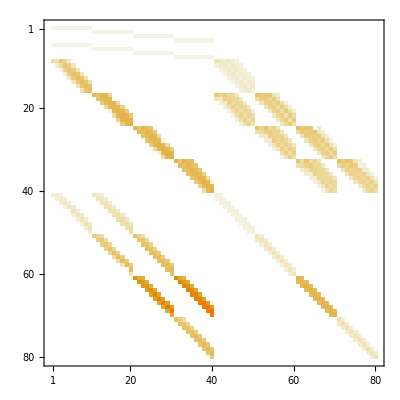

```mathematica
GraphicsRow[MatrixPlot/@Abs[A]]
```

```mathematica
MatrixPlot@Abs[A[[2]]]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/rekierj/sprouts/examples

```mathematica
Export["../slepc/A0.mtx",A[[1]]/Norm[A[[1]],"Frobenius"]]
Export["../slepc/A1.mtx",A[[2]]/Norm[A[[1]],"Frobenius"]]
```

Export::type: SparseArray[Automatic,{80},0,{1,{{0,1},{{5}}},{1}}] cannot be exported to the MatrixMarket format.

$Failed

../slepc/A1.mtx

```mathematica
LinearSolve[A[[2]]/Norm[A[[1]]],A[[1]]/Norm[A[[1]]]]
```

{0.461909-0.0112007 ⅈ,0.485589-0.00271795 ⅈ,0.0422257+0.0103334 ⅈ,0.0130528+0.00318794 ⅈ,-0.00372829+0.000627508 ⅈ,0.00125398-0.000338008 ⅈ,-0.000379585+0.000199852 ⅈ,0.000104164-0.000106798 ⅈ,-0.0000271412+0.0000399236 ⅈ,3.49616×10^-7-0.0000251804 ⅈ,-0.0113881-0.00302005 ⅈ,0.00881328+0.00264034 ⅈ,0.00673753+0.00139269 ⅈ,-0.00648825-0.00180159 ⅈ,0.00360182+0.00124585 ⅈ,-0.00193466-0.000698449 ⅈ,0.000913192+0.000333455 ⅈ,-0.000359886-0.00013214 ⅈ,0.000135543+0.0000480525 ⅈ,-0.0000304778-8.15929×10^-6 ⅈ,-0.00299345-0.000960297 ⅈ,0.000172106+0.000162038 ⅈ,0.00384466+0.00120048 ⅈ,-0.00111613-0.000509767 ⅈ,-0.000131258+0.0000344631 ⅈ,0.00052139+0.000176763 ⅈ,-0.000539776-0.000200726 ⅈ,0.000350613+0.000140871 ⅈ,-0.000180171-0.0000739179 ⅈ,0.0000720206+0.0000300956 ⅈ,-0.000670379-0.000219959 ⅈ,-0.000481881-0.000133391 ⅈ,0.00100505+0.000354329 ⅈ,0.00030972+0.0000571221 ⅈ,-0.000321611-0.000117966 ⅈ,0.000258673+0.000102457 ⅈ,-0.000066854-0.0000349879 ⅈ,-0.0000410783-9.43168×10^-6 ⅈ,0.0000537976+0.000018585 ⅈ,-0.0000454336-0.0000167565 ⅈ,0.257022+0.0808193 ⅈ,-0.72132-0.138442 ⅈ,0.257048+0.0760081 ⅈ,-0.151714-0.0531284 ⅈ,0.0732704+0.0273999 ⅈ,-0.034002-0.0132598 ⅈ,0.0158377+0.00642625 ⅈ,-0.00660864-0.00285113 ⅈ,0.00303792+0.00135018 ⅈ,-0.00120419-0.000739704 ⅈ,0.0930776+0.0291069 ⅈ,-0.0183753-0.00853241 ⅈ,-0.0587982-0.0155738 ⅈ,0.0836561+0.0280656 ⅈ,-0.0687727-0.0252217 ⅈ,0.0448148+0.0175491 ⅈ,-0.0264265-0.0105616 ⅈ,0.014272+0.00588955 ⅈ,-0.00667292-0.00274722 ⅈ,0.00340443+0.00152478 ⅈ,0.0244618+0.00745192 ⅈ,0.023856+0.0052646 ⅈ,-0.037351-0.0115706 ⅈ,0.0211838+0.00779838 ⅈ,0.0046249+0.000311826 ⅈ,-0.0148756-0.0044458 ⅈ,0.0157114+0.00519317 ⅈ,-0.012076-0.004109 ⅈ,0.00675202+0.00235652 ⅈ,-0.0032581-0.00110145 ⅈ,0.00704409+0.00186085 ⅈ,0.0171777+0.00396058 ⅈ,-0.0142189-0.00444137 ⅈ,-0.00812828-0.0013372 ⅈ,0.0132437+0.00361402 ⅈ,-0.00857336-0.00274863 ⅈ,0.00145934+0.000799714 ⅈ,0.0021884+0.000403695 ⅈ,-0.00300179-0.000769114 ⅈ,0.00105458+0.000277091 ⅈ}

## Solve and post-process

```mathematica
(*target=(*1.306078;*)(*0.611984935*)1;*)
target=0.8944
target=-0.898134343+ⅈ 0.006765470
```

0.8944

-0.898134+0.00676547 ⅈ

```mathematica
{eig,eigv}=Sort@Eigensystem[{A⟦1⟧,-A⟦2⟧}]//Chop;
eigv=Delete[eigv,Position[eig,ComplexInfinity]];
eig=Delete[eig,Position[eig,ComplexInfinity]];
pos=Nearest[eig->Automatic,target,1][[1]];
```

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair target and -3.03061×10^8.

```mathematica
eig⟦pos⟧
eigv⟦pos⟧;
```

-0.90378+0.0395391 ⅈ

```mathematica
Select[eig,-0.91<Re[#]<-0.88&]
```

{-0.908719+2.9862 ⅈ,-0.884412+0.832022 ⅈ,-0.881105+0.572268 ⅈ,-0.905129+0.47847 ⅈ,-0.896237+0.385059 ⅈ,-0.897953+0.279484 ⅈ,-0.90378+0.0395391 ⅈ}

```mathematica
SetDirectory[NotebookDirectory[]];
Reeigv=Import["../slepc/Real_Eigenvec.dat"];
Imeigv=Import["../slepc/Imag_Eigenvec.dat"];
eigv=(*Most@*)(Reeigv+I Imeigv)ᵀ;
eig=Import["../slepc/eigenvalues.dat"];
eig=Table[eig[[i,1]]+I eig[[i,2]],{i,1,Length[eig]}];
```

```mathematica
pos=1
```

1

```mathematica
sol=LinearSolve[A[[2]],A[[1]]];
```

```mathematica
(* extract components from solution *)
ClearAll[out,outnull]
Block[{list,coef,assoc=<||>},
Table[
list[layer]=Sprouts`layout⟦layer⟧;
coef[layer]=Chop@GetComponent[sol,list[layer],layer,Sprouts`layout⟦layer⟧,Sprouts`nr];
(*coef[layer]=Chop@GetComponent[eigv⟦pos⟧,list[layer],layer,Sprouts`layout⟦layer⟧,Sprouts`nr];*)
AppendTo[assoc,AssociationThread[list[layer],coef[layer]]]
,{layer,1,Sprouts`nlayers}];
out=assoc;
]
outnull=Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ-1,𝓂]]~Join~Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ+1,𝓂]];
AppendTo[out,outnull];
```

```mathematica
ClearAll[NChebevalC]
NChebevalC[c_][x_]:=NChebeval[N[Re[c]]][x]+ⅈ NChebeval[N[Im[c]]][x]
xk=Cos[((2Range[1,Sprouts`nr]-1)π)/(2Sprouts`nr)]//N;
rk=Sprouts`rfu[1][xk];
```

```mathematica
<<MaTeX`
```

```mathematica
(* plot chosen component *)
data=NChebevalC[P[2,2]/.out][rk];
interp=Interpolation[{rk,data}ᵀ];
Show[Plot[{Callout[Re[interp[r]],MaTeX["\\text{Real.}"],Below],Callout[Im[interp[r]],MaTeX["\\text{Imag.}"]]},{r,0,1},PlotRange->{{0,1},All}],ListPlot[{{rk,Re[data]}ᵀ,{rk,Im[data]}ᵀ}],PlotLabel->MaTeX["P_{2,2}(r)"]]
```

-Graphics-

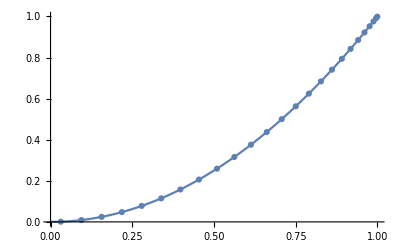

```mathematica
(* plot chosen component *)
data=NChebevalC[P[2,2]/.out][rk];
interp=Interpolation[{rk,data}ᵀ];
Show[Plot[{Abs[interp[r]]},{r,0,1},PlotRange->{{0,1},All}],ListPlot[{{rk,Abs[data]}ᵀ}],PlotLabel->MaTeX["|P_{2,2}(r)|"]]
```

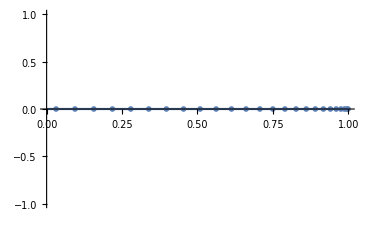

```mathematica
(* plot chosen component *)
data=NChebevalC[T[3,2]/.out][rk];
interp=Interpolation[{rk,data}ᵀ];
Show[Plot[{Abs[interp[r]]},{r,0,1},PlotRange->{{0,1},All}],ListPlot[{{rk,Abs[data]}ᵀ}],PlotLabel->MaTeX["|T_{3,2}(r)|"]]
```

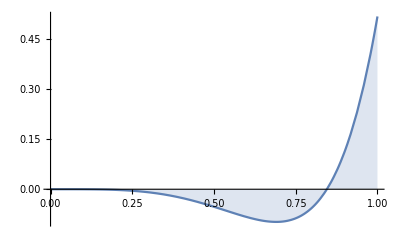

-0.000159627

```mathematica
(*(* Compute angular momentum *)
dataAM=rk^3 NChebevalC[T[1,1]/.out][rk];
interpAM=Interpolation[{rk,dataAM}ᵀ];
Plot[Re[interpAM[r]],{r,0,1},Filling->Axis,PlotRange->All]
8/3 π NIntegrate[Re[interpAM[r]],{r,0,1}]*)
```

```mathematica
(* Not working atm *)
(*(* Compute angular momentum *)
r3ck=NChebckf[r^3,r,Sprouts`nr];
TimesCheb[r3ck,T[1,1]/.out];
I0Cheb[%,{0,1}]*)
```

## Plot fields

```mathematica
ClearAll[up,ut,upint,utint,urint,ucint,upintconj,ucintconj,urintconj,utintconj,uout]
ClearAll[bp,bt,bpint,btint,brint,bcint,bpintconj,bcintconj,brintconj,btintconj,bout]
gridr=N@Subdivide[Sequence@@Sprouts`layer[1],100];
Block[{mode=pos,ℓ,𝓂,head,subset=Sprouts`layout⟦1⟧,listcomp,comp},
listcomp=GetComponent[(*solution*)eigv⟦mode⟧,subset,1,Sprouts`layout⟦1⟧,Sprouts`nr,Coordinates->"Spherical"];
Table[
head=Head[subset⟦i⟧];ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
comp=listcomp⟦i⟧;
Which[
SameQ[head,P],
up[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
upint[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]}ᵀ];
upintconj[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]*}ᵀ];
urint[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upint[ℓ,𝓂][#]]&;
urintconj[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upintconj[ℓ,𝓂][#]]&;
ucint[ℓ,𝓂]=Evaluate[(upint[ℓ,𝓂][#])/#+upint[ℓ,𝓂]'[#]]&;
ucintconj[ℓ,𝓂]=Evaluate[(upintconj[ℓ,𝓂][#])/#+upintconj[ℓ,𝓂]'[#]]&,
SameQ[head,T],
ut[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
utint[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]}ᵀ];
utintconj[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]*}ᵀ]
];
uout[-1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]-ⅈ utint[ℓ,𝓂][#])]&;uout[0][ℓ,𝓂]=Evaluate[urint[ℓ,𝓂][#]]&;uout[+1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]+ⅈ utint[ℓ,𝓂][#])]&;

,{i,1,Length[subset]}]
];
```

```mathematica
utint[ℓ_,𝓂_][r_]:=0;
urint[ℓ_,𝓂_][r_]:=0;
ucint[ℓ_,𝓂_][r_]:=0;
upint[ℓ_,𝓂_][r_]:=0;
utintconj[ℓ_,𝓂_][r_]:=0;
urintconj[ℓ_,𝓂_][r_]:=0;
ucintconj[ℓ_,𝓂_][r_]:=0;
upintconj[ℓ_,𝓂_][r_]:=0;
```

```mathematica
ClearAll[Y]
Y[ℓ_,𝓂_,θ_,ϕ_]:=Y[ℓ,𝓂,θ,ϕ]=√((4π)/(2 ℓ+1))SphericalHarmonicY[ℓ,𝓂,θ,ϕ]
```

```mathematica
gridθ=Range[0.,π,π/100];
Block[{ℓ,𝓂,subset=Sprouts`layout⟦1⟧,ϕ=0},
gridur=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
Re@Which[
SameQ[{ℓ,𝓂},{0,0}],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
SameQ[𝓂,0],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
True,2*uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ]
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduθ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduϕ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
];
griduρ=(gridurᵀ*Sin[gridθ]+griduθᵀ*Cos[gridθ])ᵀ;
griduz=(gridurᵀ*Cos[gridθ]-griduθᵀ*Sin[gridθ])ᵀ;
```

```mathematica
coord[r_,θ_,ϕ_]:=
{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ] };
ClearAll[StreamMeridPlot,MeridPlot]
StreamMeridPlot[rj_List,θk_List,ϕ_,{v1_,v2_,s_},opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[s]≠0,Max@Abs[s],1]},
tab=Flatten[Table[{{√((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧},{{v1⟦j,k⟧,v2⟦j,k⟧},s⟦j,k⟧}},{j,1,nr},{k,1,nθ}],1];
tab;
ListStreamDensityPlot[tab,ColorFunction->(Lighter[ColorData["ThermometerColors"][Rescale[#,{-max,max} ]],0.1]&),ColorFunctionScaling->False,opts]]
coord[r_,θ_,ϕ_]:=
{Abs[r] Cos[ϕ] Sin[θ],Abs[r] Sin[θ] Sin[ϕ],Abs[r] Cos[θ] };
MeridPlot[rj_List,θk_List,mat_,ϕ_,opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[mat]≠0,Max@Abs[mat],1]},
tab=Flatten[Table[{Sign[rj⟦j⟧] √((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧,mat⟦j,k⟧},{j,1,nr},{k,1,nθ}],1];
ListContourPlot[tab,ColorFunction->(ColorData["ThermometerColors"][Rescale[#,{-max,max} ]]&),ColorFunctionScaling->False,opts]]
```

```mathematica
<<MaTeX`
```

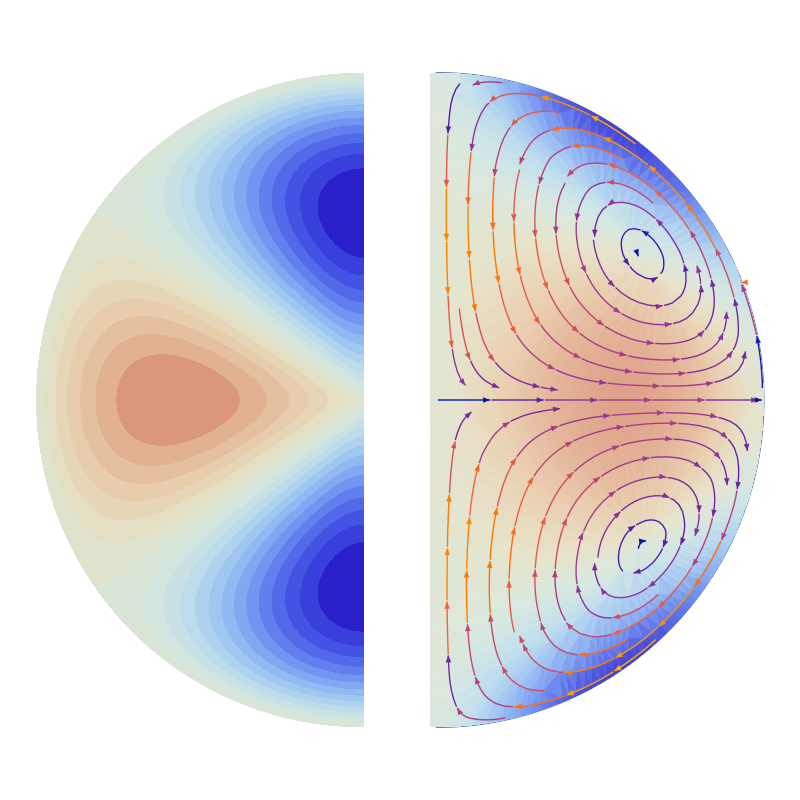

```mathematica
GraphicsGrid[{{
Show[MeridPlot[-gridr,gridθ,gridur,0,AspectRatio->2,PlotRangePadding->None,Frame->False,Contours->20,PlotRange->All,ContourStyle->None,RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]]],PlotLabel->MaTeX["\\text{Radial velocity}",Magnification->1]],
Show[StreamMeridPlot[gridr,gridθ,0,{griduρ,griduz,griduϕ},AspectRatio->2,PlotRangePadding->None,Frame->False,PlotRange->All,StreamScale->Medium,StreamStyle->Black,RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]]],PlotLabel->MaTeX["\\text{Velocity}",Magnification->1]]}},PlotLabel->MaTeX["\\omega="<>ToString[ω/.(*parameters*)ω->Chop@N[eig⟦pos⟧,5]],Magnification->1.5],Spacings->0]
```

```mathematica
With[{ℓ=4,𝓂=0},
sol=NSolve[(1-σ^2)D[LegendreP[ℓ,𝓂,σ], σ]==𝓂 LegendreP[ℓ,𝓂,σ],σ];
2σ /. sol
]
```

{-2.,-1.30931,0.,1.30931,2.}

```mathematica
N[eig⟦pos⟧,10]
```

0.894427

```mathematica
0.8944271909999169
```